# Contractions with K_i

## Monopole

```mathematica
K0i=(16π ( nx ni - xi)/(3(1- nx^2)) )( 2y - 2y^2 + 3y^2 Log[y])
```

(16 π (ni nx-xi) (2 y-2 y^2+3 y^2 Log[y]))/(3 (1-nx^2))

```mathematica
K0j=(16π ( nx nj - xj)/(3(1- nx^2)) )( 2y - 2y^2 + 3y^2 Log[y])
```

(16 π (nj nx-xj) (2 y-2 y^2+3 y^2 Log[y]))/(3 (1-nx^2))

```mathematica
K0sq = (K0i*K0i//Expand)/.ni^2->1/. ni xi -> nx/. xi^2->1 /. y->(1-nx)/2//FullSimplify
```

-(16 (-1+nx) π^2 (-2-2 nx+Log[8]+3 nx Log[(1-nx)/2]-3 Log[1-nx])^2)/(9 (1+nx))

```mathematica
Eq1=K0sq/.nx->Cos[ζ]//FullSimplify
```

16/9 π^2 (-2+Log[8]-3 Log[1-Cos[ζ]]+Cos[ζ] (-2+3 Log[Sin[ζ/2]^2]))^2 Tan[ζ/2]^2

```mathematica
TeXForm[Eq1]
```

\frac{16}{9} \pi ^2 \tan ^2\left(\frac{\zeta }{2}\right) \left(-3 \log
   (1-\cos (\zeta ))+\cos (\zeta ) \left(3 \log \left(\sin
   ^2\left(\frac{\zeta }{2}\right)\right)-2\right)-2+\log (8)\right)^2

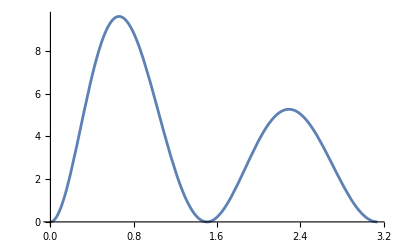

```mathematica
Plot[Eq1,{ζ,0.001,π-0.001},PlotRange->All]
```

```mathematica
root1=FindRoot[Eq1==0, {ζ,0.1}]
```

{ζ→1.06838×10^-8}

```mathematica
root2=FindRoot[Eq1==0, {ζ,1.5}]
```

{ζ→1.50357}

```mathematica
max1=FindRoot[Eq1==9.60, {ζ,0.5}]
```

{ζ→0.648186}

```mathematica
max2=FindRoot[Eq1==5.26, {ζ,2.3}]
```

{ζ→2.30724}

```mathematica
degrees = (2.307236748464649*180)/π
```

132.195

```mathematica
FindRoot[K0sq==0, {nx,0}]
```

{nx→0.0671785}

## Dipole

```mathematica
b1=π( (A1v^2)(1 -12y) + A1A2 (A1A2 + 12 A1A2 y^2 + 4 nv y (1 +y (5-6y))))/(6 A1v (1-y)y)+ 2π( (A1A2)^2 -(A1v^2) + 2 (A1A2) nv(1-y))y Log[y]/( A1v (1-y)^2)
```

(π (A1v^2 (1-12 y)+A1A2 (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y))))/(6 A1v (1-y) y)+(2 π (A1A2^2-A1v^2+2 A1A2 nv (1-y)) y Log[y])/(A1v (1-y)^2)

```mathematica
b2=- 2π( (A1A2)+12 A1A2 y^2 +4 nv y (1+y (5-6y)))/(3A1v )- 8π( (A1A2)+2 nv(1-y))y^2 Log[y]/( A1v (1-y))
```

-(2 π (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y)))/(3 A1v)-(8 π (A1A2+2 nv (1-y)) y^2 Log[y])/(A1v (1-y))

```mathematica
(K1i = b1 A1i +b2 A2i)
```

A1i ((π (A1v^2 (1-12 y)+A1A2 (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y))))/(6 A1v (1-y) y)+(2 π (A1A2^2-A1v^2+2 A1A2 nv (1-y)) y Log[y])/(A1v (1-y)^2))+A2i (-(2 π (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y)))/(3 A1v)-(8 π (A1A2+2 nv (1-y)) y^2 Log[y])/(A1v (1-y)))

```mathematica
K1iSC =(2π  (ni(1-2z)-xi)/(3(1-z)))((z-1)(6z+1)-6z Log[z])
```

(2 π (-xi+ni (1-2 z)) ((-1+z) (1+6 z)-6 z Log[z]))/(3 (1-z))

```mathematica
K1K1 = (K1iSC *K1iSC //Expand)/.ni xi->nx/. ni^2->1/. xi^2->1//FullSimplify
```

(8 π^2 (1+2 (-1+z) z+nx (-1+2 z)) (1+(5-6 z) z+6 z Log[z])^2)/(9 (-1+z)^2)

```mathematica
K1sq=(K1i*K1i//Expand)/. A2i^2->A2A2/. A1i^2-> A1A1 /. A1i A2i->A1A2  //FullSimplify
```

1/(36 A1v^2 (-1+y)^4 y^2)π^2 ((-1+y)^2 (8 (-1+y) y (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y)) (A1A2 A1v^2 (1-12 y)-8 A2A2 nv (-1+y)^2 y^2 (1+6 y)+4 A1A2^2 nv y (1+(5-6 y) y)+A1A2^3 (1+12 y^2)+2 A1A2 A2A2 (-1+y) y (1+12 y^2))+A1A1 (A1v^2 (1-12 y)+A1A2 (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y)))^2)-24 (-1+y) y^2 (A1A1 (A1A2^2-A1v^2-2 A1A2 nv (-1+y)) (A1v^2 (1-12 y)+A1A2 (A1A2+12 A1A2 y^2+4 nv y (1+(5-6 y) y)))+8 (-1+y) y (16 A2A2 nv^2 (-1+y)^3 y^2 (1+6 y)+A1A2^4 (1+12 y^2)+2 A1A2^3 nv (1+y+22 y^2-24 y^3)+2 A1A2^2 y (-3 A1v^2 (1+y)+(-1+y) (A2A2+12 A2A2 y^2+4 nv^2 (-1+y) (1+6 y)))+A1A2 nv (-1+y) (4 A2A2 y (1+y+22 y^2-24 y^3)+A1v^2 (-1+2 y (7+6 y))))) Log[y]+144 y^4 (A1A1 (-A1A2^2+A1v^2+2 A1A2 nv (-1+y))^2+8 (A1A2-2 nv (-1+y)) (-1+y) y (A1A2^3-A1A2 A1v^2-2 A1A2^2 nv (-1+y)+2 A1A2 A2A2 (-1+y) y-4 A2A2 nv (-1+y)^2 y)) Log[y]^2)

```mathematica
K1sq/.A1A2->0/.A2A2->0//Simplify
```

(A1A1 A1v^2 π^2 (1-13 y+12 y^2-12 y^2 Log[y])^2)/(36 (-1+y)^4 y^2)

```mathematica
K1squared=((K1sq/. A1A1 ->( 1-nx^2  )/. A2A2-> (1-nv^2 )/.A1A2 ->vx - (nv nx)/.y->(1-nx)/2)//FullSimplify)
```

1/(9 (1+nx)^4 (A1v-A1v nx)^2)4 (-1+nx^2) π^2 ((1+nx)^2 (-A1v^4 (5-6 nx)^2+(nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx)^2 (-1+nv^2+nx^2-2 nv nx vx+vx^2))+12 Log[(1-nx)/2] ((-1+nx)^2 (1+nx) (A1v^4 (-5+6 nx)+(nv+vx) (nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx) (-1+nv^2+nx^2-2 nv nx vx+vx^2))+3 (-1+nx)^4 (-A1v^4+(nv+vx)^2 (-1+nv^2+nx^2-2 nv nx vx+vx^2)) Log[(1-nx)/2]))

```mathematica
K1K1Simp=Collect[K1squared/.-1+nv^2+nx^2-2 nv nx vx+vx^2-> α
 /. nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx->β/. ((-1+nx)^2 (1+nx) (A1v^4 (-5+6 nx)+(nv+vx) α β)+3 (-1+nx)^4 (-A1v^4+(nv+vx)^2 α) Log[(1-nx)/2])-> γ, FullSimplify]
```

(4 (-1+nx^2) π^2 ((1+nx)^2 (-A1v^4 (5-6 nx)^2+α β^2)+12 γ Log[(1-nx)/2]))/(9 (1+nx)^4 (A1v-A1v nx)^2)

```mathematica
TeXForm[K1K1Simp]
```

\frac{4 \pi ^2 \left(\text{nx}^2-1\right) \left((\text{nx}+1)^2
   \left(\alpha  \beta ^2-\text{A1v}^4 (5-6 \text{nx})^2\right)+12
   \gamma  \log \left(\frac{1-\text{nx}}{2}\right)\right)}{9
   (\text{nx}+1)^4 (\text{A1v}-\text{A1v} \text{nx})^2}

```mathematica
K1squared/.vx->-nx/.nv->-1//Simplify
```

-(4 A1v^2 π^2 (-5+nx+6 nx^2-6 (-1+nx)^2 Log[(1-nx)/2])^2)/(9 (-1+nx) (1+nx)^3)

```mathematica
Collect[K1squared,{nx->1-2y,Log[y]},Simplify]
```

1/(9 (1+nx)^4 (A1v-A1v nx)^2)4 (-1+nx^2) π^2 ((1+nx)^2 (-A1v^4 (5-6 nx)^2+(nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx)^2 (-1+nv^2+nx^2-2 nv nx vx+vx^2))+12 Log[(1-nx)/2] ((-1+nx)^2 (1+nx) (A1v^4 (-5+6 nx)+(nv+vx) (nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx) (-1+nv^2+nx^2-2 nv nx vx+vx^2))+3 (-1+nx)^4 (-A1v^4+(nv+vx)^2 (-1+nv^2+nx^2-2 nv nx vx+vx^2)) Log[(1-nx)/2]))

```mathematica
EqK1 = Collect[K1squared ,{A1v}]
```

1/(9 (1+nx)^4 (A1v-A1v nx)^2)4 (-1+nx^2) π^2 ((1+nx)^2 (-A1v^4 (5-6 nx)^2+(nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx)^2 (-1+nv^2+nx^2-2 nv nx vx+vx^2))+12 Log[(1-nx)/2] ((-1+nx)^2 (1+nx) (A1v^4 (-5+6 nx)+(nv+vx) (nv (4+nx (-7+2 nx))+(4+3 (-2+nx) nx) vx) (-1+nv^2+nx^2-2 nv nx vx+vx^2))+3 (-1+nx)^4 (-A1v^4+(nv+vx)^2 (-1+nv^2+nx^2-2 nv nx vx+vx^2)) Log[(1-nx)/2]))

## Special elections for

## Case:

```mathematica
EqnV =K1squared/. nx->-vx/. nv->-1
```

(4 π^2 (-1+vx^2) (-A1v^4 (1-vx)^2 (5+6 vx)^2+12 Log[(1+vx)/2] (A1v^4 (-5-6 vx) (-1-vx)^2 (1-vx)-3 A1v^4 (-1-vx)^4 Log[(1+vx)/2])))/(9 (1-vx)^4 (A1v+A1v vx)^2)

```mathematica
T1=EqnV//Expand
```

(100 A1v^4 π^2)/(9 (1-vx)^4 (A1v+A1v vx)^2)+(40 A1v^4 π^2 vx)/(9 (1-vx)^4 (A1v+A1v vx)^2)-(112 A1v^4 π^2 vx^2)/(3 (1-vx)^4 (A1v+A1v vx)^2)-(88 A1v^4 π^2 vx^3)/(9 (1-vx)^4 (A1v+A1v vx)^2)+(380 A1v^4 π^2 vx^4)/(9 (1-vx)^4 (A1v+A1v vx)^2)+(16 A1v^4 π^2 vx^5)/(3 (1-vx)^4 (A1v+A1v vx)^2)-(16 A1v^4 π^2 vx^6)/((1-vx)^4 (A1v+A1v vx)^2)+(80 A1v^4 π^2 Log[(1+vx)/2])/(3 (1-vx)^4 (A1v+A1v vx)^2)+(176 A1v^4 π^2 vx Log[(1+vx)/2])/(3 (1-vx)^4 (A1v+A1v vx)^2)-(64 A1v^4 π^2 vx^2 Log[(1+vx)/2])/(3 (1-vx)^4 (A1v+A1v vx)^2)-(352 A1v^4 π^2 vx^3 Log[(1+vx)/2])/(3 (1-vx)^4 (A1v+A1v vx)^2)-(112 A1v^4 π^2 vx^4 Log[(1+vx)/2])/(3 (1-vx)^4 (A1v+A1v vx)^2)+(176 A1v^4 π^2 vx^5 Log[(1+vx)/2])/(3 (1-vx)^4 (A1v+A1v vx)^2)+(32 A1v^4 π^2 vx^6 Log[(1+vx)/2])/((1-vx)^4 (A1v+A1v vx)^2)+(16 A1v^4 π^2 Log[(1+vx)/2]^2)/((1-vx)^4 (A1v+A1v vx)^2)+(64 A1v^4 π^2 vx Log[(1+vx)/2]^2)/((1-vx)^4 (A1v+A1v vx)^2)+(80 A1v^4 π^2 vx^2 Log[(1+vx)/2]^2)/((1-vx)^4 (A1v+A1v vx)^2)-(80 A1v^4 π^2 vx^4 Log[(1+vx)/2]^2)/((1-vx)^4 (A1v+A1v vx)^2)-(64 A1v^4 π^2 vx^5 Log[(1+vx)/2]^2)/((1-vx)^4 (A1v+A1v vx)^2)-(16 A1v^4 π^2 vx^6 Log[(1+vx)/2]^2)/((1-vx)^4 (A1v+A1v vx)^2)

```mathematica
Collect[T1, {A1v}]//FullSimplify
```

-(4 A1v^2 π^2 (5+vx-6 vx^2+6 (1+vx)^2 Log[(1+vx)/2])^2)/(9 (-1+vx)^3 (1+vx))

```mathematica
EQnv = K1K1/.z-> (1-nx)/2/. nx->-vx/. nv->-1
```

(8 π^2 (1-vx^2+(1+vx) (-1+(1+vx)/2)) (1+1/2 (1+vx) (5-3 (1+vx))+3 (1+vx) Log[(1+vx)/2])^2)/(9 (-1+(1+vx)/2)^2)

```mathematica
Eq2 = EQnv/. vx ->-Cos[ζ]//FullSimplify
```

1/9 π^2 (5+2 Cos[ζ]-3 Cos[2 ζ]-12 (-1+Cos[ζ]) Log[Sin[ζ/2]^2])^2 Tan[ζ/2]^2

```mathematica
TeXForm[Eq2]
```

\frac{1}{9} \pi ^2 \tan ^2\left(\frac{\zeta }{2}\right) \left(2 \cos
   (\zeta )-3 \cos (2 \zeta )-12 (\cos (\zeta )-1) \log \left(\sin
   ^2\left(\frac{\zeta }{2}\right)\right)+5\right)^2

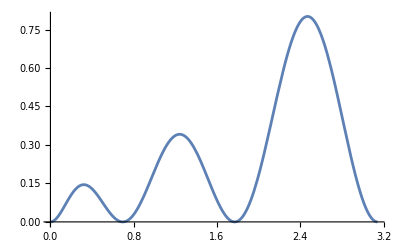

```mathematica
Plot[Eq2,{ζ,0.001,π-0.001},PlotRange->All]
```

```mathematica
rootK1=FindRoot[Eq2==0, {ζ,0.1}]
```

{ζ→9.62596×10^-9}

```mathematica
rootK2=FindRoot[Eq2==0, {ζ,0.7}]
```

{ζ→0.695051}

```mathematica
rootK3=FindRoot[Eq2==0, {ζ,1.7}]
```

{ζ→1.76931}

```mathematica
rootK4=FindRoot[Eq2==0, {ζ,3}]
```

{ζ→3.14159}

```mathematica
maxK1=FindRoot[Eq2==0.145, {ζ,0.3}]
```

{ζ→0.313779}

```mathematica
maxK2=FindRoot[Eq2==0.341, {ζ,1.3}]
```

{ζ→1.25467}

```mathematica
maxK3=FindRoot[Eq2==0.8, {ζ,2.5}]
```

{ζ→2.48348}

```mathematica
degrees2 = (2.483479781113068*180)/π
```

142.293

## Case:

```mathematica
EqV = K1squared/. nx->vx/. nv->1
```

(4 π^2 (-1+vx^2) (-A1v^4 (5-6 vx)^2 (1+vx)^2+12 Log[(1-vx)/2] (A1v^4 (-1+vx)^2 (1+vx) (-5+6 vx)-3 A1v^4 (-1+vx)^4 Log[(1-vx)/2])))/(9 (1+vx)^4 (A1v-A1v vx)^2)

## Case: (This means n orthogonal to v)

```mathematica
EqOV = (EqK1/.y ->(1-nx)/2/. nv->0)//FullSimplify
```

1/(9 (1+nx)^4 (A1v-A1v nx)^2)4 (-1+nx^2) π^2 ((1+nx)^2 (-A1v^4 (5-6 nx)^2+(4+3 (-2+nx) nx)^2 vx^2 (-1+nx^2+vx^2))+12 Log[(1-nx)/2] ((-1+nx)^2 (1+nx) (A1v^4 (-5+6 nx)+(4+3 (-2+nx) nx) vx^2 (-1+nx^2+vx^2))+3 (-1+nx)^4 (-A1v^4+vx^2 (-1+nx^2+vx^2)) Log[(1-nx)/2]))